```mathematica
H = ω1  n1[t]+ω2 n2[t] +ω3 n3[t] + 2g12 Sqrt[n1[t]n2[t]]Cos[ϕ1[t]-ϕ2[t]]+2g13 Sqrt[n1[t] n3[t]]Cos[ϕ1[t]-ϕ3[t]]+2g23 Sqrt[n2[t] n3[t]]Cos[ϕ2[t]-ϕ3[t]];
Hq=({{ω1, g12, g13}, {g12, ω2, g23}, {g13, g23, ω3}});
```

```mathematica
diffs={D[n1[t],t]==D[H,ϕ1[t]],D[n2[t],t]==D[H,ϕ2[t]],D[n3[t],t]==D[H,ϕ3[t]],D[ϕ1[t],t]==-D[H,n1[t]],D[ϕ2[t],t]==-D[H,n2[t]],D[ϕ3[t],t]==-D[H,n3[t]]};
initials1={n1[0]==0.5,n2[0]==0.4,n3[0]==0.2,ϕ1[0]==0,ϕ2[0]==0,ϕ3[0]==0};
initials2={n1[t0]==0.5,n2[t0]==0.4,n3[t0]==0.2,ϕ1[t0]==0.01,ϕ2[t0]==0,ϕ3[t0]==0.0};
subs ={g12->Sqrt[2],g13->Sqrt[3],g23->1, ω1->1, ω2->2,ω3->0};
```

```mathematica
res1=NDSolve[Join[diffs,initials1]/.subs, {D[n1[t],t],D[n2[t],t],D[n3[t],t],n1[t],n2[t],n3[t],ϕ1[t],ϕ2[t],ϕ3[t]},{t,0,200}];
res2=NDSolve[Join[diffs,(initials2/.{t0->0})]/.subs, {D[n1[t],t],D[n2[t],t],D[n3[t],t],n1[t],n2[t],n3[t],ϕ1[t],ϕ2[t],ϕ3[t]},{t,0,200}];
```

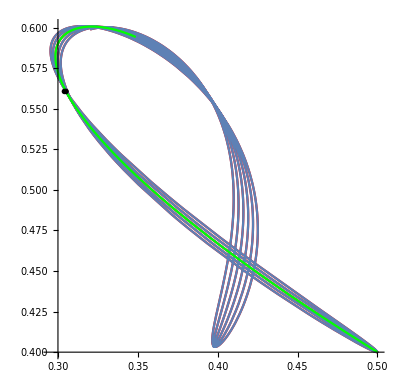

-Graphics3D-

```mathematica
p1=ParametricPlot[{n1[t],n2[t]}/.res1[[1]],{t,0,10},PlotStyle->Red];
f[t_]:=N[MatrixExp[ⅈ (Hq/.subs) t].({{Sqrt[0.5]}, {Sqrt[0.4]}, {Sqrt[0.2]}})];
p2=ParametricPlot[{Abs[f[t][[1,1]]]^2,Abs[f[t][[2,1]]]^2},{t,0,10}];
p3=ParametricPlot[{n1[t],n2[t]}/.res1[[1]],{t,0,1},PlotStyle->Green];
Show[p1,p2,p3,Graphics[{PointSize[.01],Point[{n1[t],n2[t]}/.res1[[1]]/.{t->0.63}]}],Graphics[{PointSize[.01],Point[{0.30405878329886293,.5607325247734416`}]}]]
ParametricPlot3D[{n1[t],n2[t],ϕ2[t]-ϕ3[t]}/.res1[[1]],{t,0,200}]
```

```mathematica
f[t_]:=N[MatrixExp[ⅈ (Hq/.subs) t].({{Sqrt[0.5]}, {Sqrt[0.4]}, {Sqrt[0.2]}})]
Abs[f[1][[3,1]]]
```

0.396248

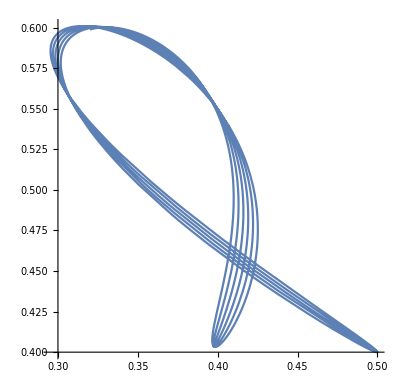

```mathematica
p2=ParametricPlot[{Abs[f[t][[1,1]]]^2,Abs[f[t][[2,1]]]^2},{t,0,10}]
```

```mathematica
eigS=N[Eigensystem[Hq/.subs]];
λ1 = eigS[[1,1]];
λ2 = eigS[[1,2]];
λ3 = eigS[[1,3]];
e1 = eigS[[2,1]];
e2 = eigS[[2,2]];
e3 = eigS[[2,3]];
a1=(Inverse[Transpose[eigS[[2]]]].({{Sqrt[0.5]}, {Sqrt[0.4]}, {Sqrt[0.2]}}))[[1,1]];
a2=(Inverse[Transpose[eigS[[2]]]].({{Sqrt[0.5]}, {Sqrt[0.4]}, {Sqrt[0.2]}}))[[2,1]];
a3=(Inverse[Transpose[eigS[[2]]]].({{Sqrt[0.5]}, {Sqrt[0.4]}, {Sqrt[0.2]}}))[[3,1]];
fnc[t_,ϵ1_,ϵ2_]:={( a1 e1 Exp[ⅈ (λ1+ϵ1) t]+ a2 e2 Exp[ⅈ (λ2+ϵ2) t]+ a3 e3 Exp[ⅈ λ3 t])*( a1 e1 Exp[-ⅈ (λ1+ϵ1) t]+ a2 e2 Exp[-ⅈ (λ2+ϵ2) t]+ a3 e3 Exp[-ⅈ λ3 t])};
```

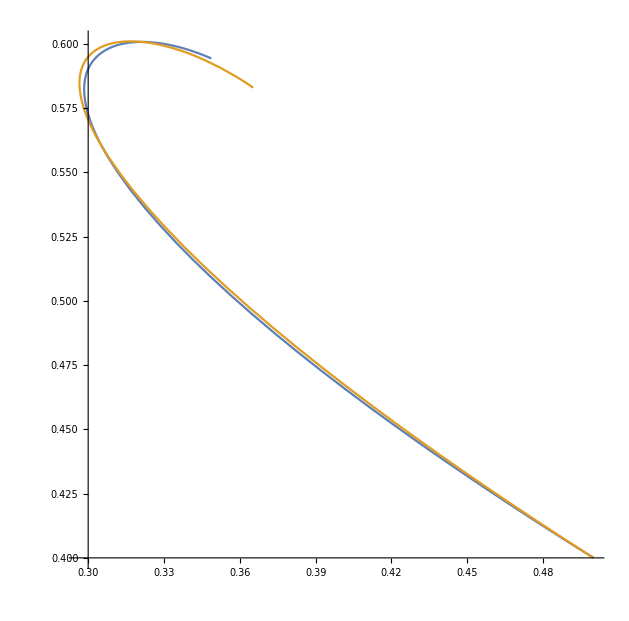

```mathematica
ParametricPlot[{fnc[t,0.00,0][[1,1;;2]],fnc[t,0.25,0][[1,1;;2]]},{t,0,1}]
```

```mathematica
pf[t_,ϕ_ ]:=(D[fnc[t,ϕ,0],ϕ][[1,1]]*D[fnc[t,ϕ,0],t][[1,2]]-D[fnc[t,ϕ,0],ϕ][[1,2]]*D[fnc[t,ϕ,0],t][[1,1]]);
Plot[pf,{t,0,1}]
```

-Graphics-

```mathematica
f[N1_,N2_,subs_]:=Module[{Hb=((H/.{ϕ1[t]->0,ϕ2[t]->0,ϕ3[t]->0,n1[t]->n1,n2[t]->n2,n3[t]->1-n1-n2})/.subs)},dn1=D[Hb, n1]/.{n1->N1, n2->N2};dn2=D[Hb,n2]/.{n1->N1, n2->N2};
a= 1-0*dn2/Sqrt[dn1*dn1+dn2*dn2];
b= -Re[dn1/dn2]+Im[dn1/dn2] +0*Sqrt[dn1*dn1+dn2*dn2];
{a,b}];
```

```mathematica
res=NDSolve[{x'[t]==f[x[t],y[t],subs][[1]],y'[t]==f[x[t],y[t],subs][[2]],x[0]==y[0]==.1},{x,y},{t,0,1}]
```

NDSolve::ndsz: At t == 0.818032, step size is effectively zero; singularity or stiff system suspected.

{{x→InterpolatingFunction[{{0., 0.818032}}, <>],y→InterpolatingFunction[{{0., 0.818032}}, <>]}}

```mathematica
ParametricPlot[{(x/.res[[1]])[t],(y/.res[[1]])[t]},{t,0,1}]
```

-Graphics-

```mathematica
(y/.res[[1]])[.557]
```

0.500361

```mathematica
Im[ⅈ]
```

1